# Second law teaching demonstration

Grey cells will initialise automatically, 
Red cells are computations that need to be executed (the can take some time for a large number of steps). 
Blue cell produce plots

## Define functions for random walk

```mathematica
step//Clear;
step[state_]:=Block[{stateN,pos,pp},
stateN=Table[0,Length[state],Length[state[[1]]]];
pos=Position[state,_?(#!=0&)];
Do[
Do[
pp=pos[[i]]+RandomChoice[{{0,0},{1,0},{0,1},{-1,0},{0,-1}}];
If[pp[[1]]==0,pp[[1]]=1;];
If[pp[[2]]==0,pp[[2]]=1;];
If[pp[[1]]>Length[state],pp[[1]]=Length[state];];
If[pp[[2]]>Length[state[[1]]],pp[[2]]=Length[state[[1]]];];
stateN[[pp[[1]],pp[[2]]]]+=1;
,
{state[[pos[[i,1]],pos[[i,2]]]]}]
,
{i,1,Length[pos]}];
Return[stateN]];
```

```mathematica
stepWmem//Clear;
stepWmem[state_]:=Block[{stateN,pos,pp},
stateN=state;
stateN[[1]]=Table[0,Length[state[[1]]],Length[state[[1,1]]]];
pos=Position[state[[1]],_?(#!=0&)];
Do[
Do[
pp=pos[[i]]+RandomChoice[{{0,0},{1,0},{0,1},{-1,0},{0,-1}}];
If[pp[[1]]==0,pp[[1]]=1;];
If[pp[[2]]==0,pp[[2]]=1;];
If[pp[[1]]>Length[state[[1]]],pp[[1]]=Length[state[[1]]];];
If[pp[[2]]>Length[state[[1,1]]],pp[[2]]=Length[state[[1,1]]];];
stateN[[1,pp[[1]],pp[[2]]]]+=1;
If[stateN[[2,pp[[1]],pp[[2]]]]==0,stateN[[2,pp[[1]],pp[[2]]]]+=1;];
,
{state[[1,pos[[i,1]],pos[[i,2]]]]}]
,
{i,1,Length[pos]}];
Return[stateN]];
```

Default plotting options:

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,RegionPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
```

## Examples

### Random walk (single unit of energy)

Define the initial state:

```mathematica
states={{Table[0,20,20],Table[0,20,20]}};
states[[1,1,10,10]]=1;
```

Evolve for N steps:

```mathematica
With[{Nsteps=10000},
Do[
states=Append[states,stepWmem[states[[-1]]]];,
Nsteps]]
```

Create animation of the random walk:

```mathematica
Animate[Show[ArrayPlot[states[[i,2]],PlotRange->{.95,1.1},Mesh->True,Epilog->Inset[Style["Steps = "<>ToString[i],20,Red],Scaled[{.1,.1}],{Left,Bottom}]],ArrayPlot[states[[i,1]],PlotRange->{.1,1.1}]],{i,1,Length[states],1}]
```

Check how many times the unit of energy visits each oscillator:

```mathematica
poss=ParallelTable[Position[Flatten[states[[i,1]]],_?(#!=0&)][[1,1]],{i,1,Length[states]}];
```

```mathematica
Histogram[poss,400,PlotRange->{{0,400},All},AspectRatio->.5]
```

### Thermal equilibrium demo

Define the initial conditions:

```mathematica
statesBar={Table[0,10,20]};
statesBar[[1,1;;10,{1,2}]]=Table[{10,10},10];
```

```mathematica
statesBar[[1]]//MatrixForm
```

(10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Evolve for N steps, and compute q and T for each step:

```mathematica
With[{Nsteps=2000},
Do[
statesBar=Append[statesBar,step[statesBar[[-1]]]];,
Nsteps]];


qA=Table[Plus@@Plus@@statesBar[[i,1;;10,1;;2]],{i,1,Length[statesBar]}];
qB=Table[Plus@@Plus@@statesBar[[i,1;;10,3;;20]],{i,1,Length[statesBar]}];
TA=Table[Plus@@Plus@@statesBar[[i,1;;10,1;;2]],{i,1,Length[statesBar]}]/20.;
TB=Table[Plus@@Plus@@statesBar[[i,1;;10,3;;20]],{i,1,Length[statesBar]}]/180.;
```

Create animation frames:

```mathematica
framesBar=Table[ArrayPlot[statesBar[[i]],
GridLines->{{{2,Blue}},None},
Epilog->{Inset[Style["q_A="<>ToString[Round[qA[[i]],1]],16,Red],Scaled[{.022,.85}],{Left,Bottom}],
Inset[Style["q_A/N_A="<>ToString[Round[TA[[i]],.1]],16,Red],Scaled[{.022,.65}],{Left,Bottom}],Inset[Style["q_B="<>ToString[Round[qB[[i]],1]],16,Blue],Scaled[{.85,.85}],{Left,Bottom}],Inset[Style["q_B/N_B="<>ToString[Round[TB[[i]],.1]],16,Blue],Scaled[{.85,.65}],{Left,Bottom}]},
ImageSize->550],{i,1,Length[statesBar],1}];

framesQ=Table[ListPlot[{qA[[1;;i]],qB[[1;;i]]},Joined->True,FrameLabel->{"Steps","q"},PlotRange->{{0,1000+1000UnitStep[i-1000]},{0,210}},AspectRatio->.5,PlotStyle->{Red,Blue}],
{i,1,Length[statesBar],1}];
framesT=Table[ListPlot[{TA[[1;;i]],TB[[1;;i]]},Joined->True,FrameLabel->{"Steps","q/N"},PlotRange->{{0,1000+1000UnitStep[i-1000]},{0,5}},AspectRatio->.5,PlotStyle->{Red,Blue}],
{i,1,Length[statesBar],1}];
```

```mathematica
Animate[
{framesBar[[i]],Column[{framesQ[[i]],framesT[[i]]}]},
{i,1,Length[framesBar],1}]
```

#### Number of microstates

```mathematica
Ω[N_,q_]:=((q+N-1)!)/(q!(N-1)!)
```

```mathematica
Ω[200,200]//N
```

5.14763×10^118

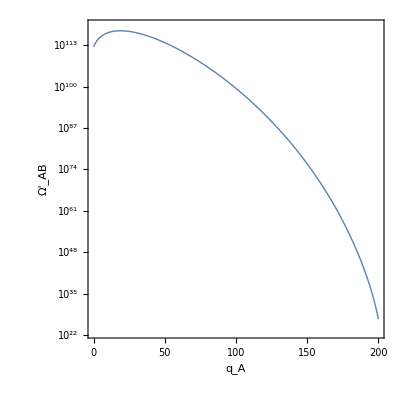

```mathematica
LogPlot[Ω[20,qA]Ω[180,200-qA],{qA,0,200},PlotRange->{10^23,10^119},
FrameLabel->{"q_A","Ω'_AB"}]
```

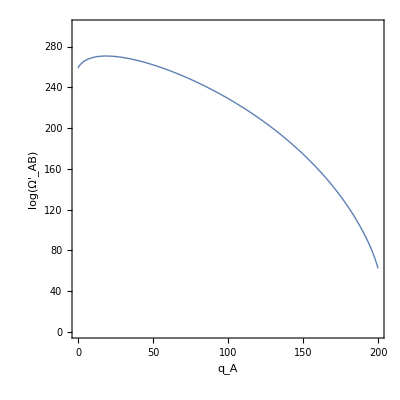

```mathematica
Plot[Log[Ω[20,qA]Ω[180,200-qA]],{qA,0,200},PlotRange->{0,300},
FrameLabel->{"q_A","log(Ω'_AB)"}]
```